```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"utils.nb"}],EvaluationElements->"InitializationCell"]
```

#### defVel (finitely generated)

```mathematica
defVel[F_Symbol,def_List/;(Length[def]≥3)]:=Module[{normals,°normals},
(* define velocity set by points in ℝ^2 *)
Subscript[F, pt]=positivelyOrient[def];
normals=rotationNormals[Subscript[F, pt]];
Subscript[F, cnds]=Simplify[normals[[#]].{x,y}≤normals[[#]].Subscript[F, pt][[#]]&/@Range[Length[normals]]];
Subscript[F, reg]=ImplicitRegion[Subscript[F, cnds],{x,y}];

Subscript[F, θMag]=hullMagFunc[Subscript[F, pt]];
(*Subscript[γ, F]=Compile[{{x,_Real,1}},Norm[x]/Subscript[F, θMag][atan2[x]]];*)
Subscript[γ, F]=Function[{x},Evaluate@Simplify[
Max[#1.x/#1.#2&@@@({rotationNormals[Subscript[F, pt]],Subscript[F, pt]}ᵀ)]
]];
Subscript[F, vζ]=vζLink[F];
Subscript[𝒩̂, F]=Subscript[F, vζ][atan2[{#⟦1⟧,#⟦2⟧}]]&;

Subscript[F, vζDisp]=Thread[rotatedPairs[Range[4]]->Range[4]]~Join~Thread[Range[4]->RotateRight@rotatedPairs[Range[4]]](* v->ζ *);
(F^°)_pt=hullToPolar[Subscript[F, pt]];
°normals=rotationNormals[(F^°)_pt];
(F^°)_cnds=Simplify[°normals[[#]].{x,y}≤°normals[[#]].(F^°)_pt[[#]]&/@Range[Length[°normals]]];
(F^°)_reg=ImplicitRegion[(F^°)_cnds,{x,y}];

(F^°)_θMag=hullMagFunc[(F^°)_pt];
Subscript[F, ζv]=ζvLink[F];
(𝒩̂)_(F^°)=If[ConeQ[#],Subscript[F, ζv][atan2[#/.λ->0.5]],Subscript[F, ζv][atan2[{#⟦1⟧,#⟦2⟧}]]]&;

Subscript[RefractedNormals, F]=Function[{ζ},
(* input: incident normal cone ζ / output: reflected normal cone *)
Module[{optVels=(F^°)_pt,optCones=(SortBy[#,First]&/@rotatedPairs[#])&[(F^°)_pt]},
If[ConeQ[ζ],
(* ζ0 is a cone *)
With[{ζ0=SortBy[{ζ/.λ->0,ζ/.λ->1},First](* temporary *)},
optVels=Select[optVels,ζ0⟦1,1⟧≤#⟦1⟧≤ζ0⟦02,1⟧&];
optCones=Select[optCones,-#⟦2,1⟧≤ζ0⟦1,1⟧≤ζ0⟦2,1⟧≤-#⟦1,1⟧||Not[Intersection[#,optVels]==={}]&];
],
(* ζ is not a cone *)
optVels=Select[optVels,#⟦1⟧==ζ⟦1⟧&];
optCones=Select[optCones,#⟦1,1⟧<ζ⟦1⟧<#⟦2,1⟧||ζ⟦1⟧==#⟦1,1⟧==#⟦2,1⟧&]
];
optVels~Join~(λ#1+(1-λ)#2&@@@optCones)
]
];
Subscript[RefractedVelocities, F]=Function[{ζ,n},With[{θ=N@VectorAngle[n,{0,1}]},
(* input: incident normal cone ζ & normal vect to incident plane / output: reflected velocity *)
Module[{optVecs=ℛ[θ].#&/@(F^°)_pt,optCones=SortBy[#,First]&/@rotatedPairs[ℛ[θ].#&/@(F^°)_pt]},
If[ConeQ[ζ],
(* ζ0 is a cone *)
Block[{ζ0=ℛ[θ].ζ},
ζ0=SortBy[{#/.λ->0,#/.λ->1}&@ζ0,First&](* temporary *);
optVecs=Select[optVecs,ζ0⟦1,1⟧≤-#⟦1⟧≤ζ0⟦02,1⟧&];
optCones=Select[optCones,-#⟦2,1⟧≤ζ0⟦1,1⟧≤ζ0⟦2,1⟧≤-#⟦1,1⟧||Not[Intersection[#,optVecs]==={}]&];
],
(* ζ is not a cone *)
With[{ζ0=ℛ[θ].ζ},
optVecs=Select[optVecs,#⟦1⟧==ζ0⟦1⟧&];
optCones=Select[optCones,#⟦1,1⟧<ζ0⟦1⟧<#⟦2,1⟧||ζ0⟦1⟧==#⟦1,1⟧==#⟦2,1⟧&]
]
];
ℛ[-θ].#&/@(𝒩̂)_(F^°)/@Join[optVecs,(λ#1+(1-λ)#2&@@@optCones)]
]
]];
]
clearVel[F_Symbol]:=Do[v=.,{v,{Subscript[F, pt],Subscript[F, ineq],Subscript[F, reg],(F^°)_pt,(F^°)_ineq,(F^°)_reg}}]
```

#### Ex. 1 (Working)

```mathematica
First@Timing@Quiet@defVel[F0,{{-1,-1},{-1,1},{1,-1},{1,1},{2,0},{-1.5,0}}]
First@Timing@Quiet@defVel[F1,1.5{{0,1},{1,0},{0,-1},{-1,0}}]
GraphicsRow[LabeledPolarHullPlot/@{F0,F1}]
```

0.03125

0.015625

-Graphics-

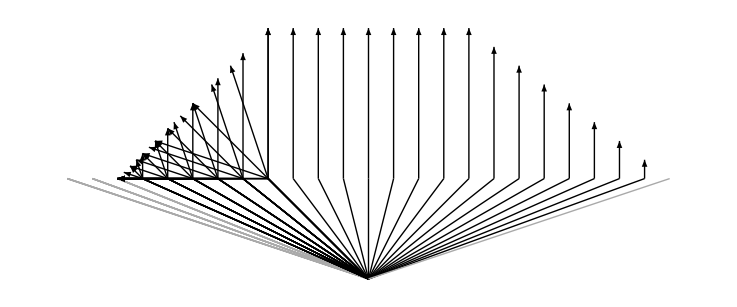

```mathematica
Show[Graphics[{
Arrowheads[Small],
Table[
Module[{x0={0,-2},T=4,t=-.1,y0,v0,ζ0,ζ2s,v2s},
y0={t0,0};
t=Subscript[γ, F0][y0-x0];
v0=(y0-x0)/t;
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F0][v0](* points in normal cone properly scaled *);
(* calculate refracted angles with optimality conditions *)
ζ2s=Subscript[RefractedNormals, F1][ζ0];
v2s=Select[discretize/@(𝒩̂)_(F1^°)/@ζ2s,NonNegative@Last@#&];


If[T>Subscript[γ, F0][y0-x0],
{Black,Line[{x0,y0}],Tooltip[Arrow[{y0,(y0+(T-Subscript[γ, F0][y0-x0])#)}],{v0}]},
{Lighter@Gray,Line[{x0,y0}]}
]&/@v2s

],
{t0,-6,6,0.5}
]}]]
```

```mathematica
Reverse[Show[{
Graphics[{Black,InfiniteLine[{0,0},{1,0}],Thick,Dashed,InfiniteLine[{0,0},{0,1}]}],
LabeledPolarPlot[F1,"(1)",TranslationTransform[#]@*ScalingTransform[{-1,-1}]],
Graphics[{Thick,Red,Arrow[{{0,0},#}]}]
},Axes->False,PlotRange->{1.5{-1,1},2{-0.5,1}},AspectRatio->{1,1},ImageSize->300]&/@Select[(F0^°)_pt,0<atan2[#]<π&]]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
First@Timing@Quiet@defVel[F1,{{-1,-1},{-1,1},{1,-1},{1,1},{2,0},{-1.5,0}}]
First@Timing@Quiet@defVel[F0,1.5{{0,1},{1,0},{0,-1},{-1,0}}]
GraphicsRow[LabeledPolarHullPlot/@{F0,F1}]
```

0.

0.

-Graphics-

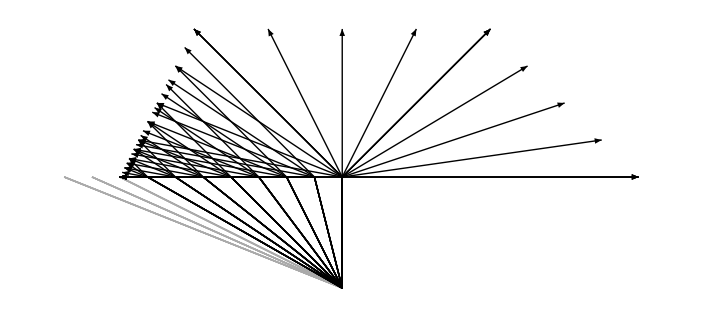

```mathematica
Show[Graphics[{
Arrowheads[Small],
Table[
Module[{x0={0,-2},T=4,t=-.1,y0,v0,ζ0,ζ2s,v2s},
y0={t0,0};
t=Subscript[γ, F0][y0-x0];
v0=(y0-x0)/t;
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F0][v0](* points in normal cone properly scaled *);
(* calculate refracted angles with optimality conditions *)
ζ2s=Subscript[RefractedNormals, F1][ζ0];
v2s=Select[discretize/@(𝒩̂)_(F1^°)/@ζ2s,NonNegative@Last@#&];


If[T>Subscript[γ, F0][y0-x0],
{Black,Line[{x0,y0}],Tooltip[Arrow[{y0,(y0+(T-Subscript[γ, F0][y0-x0])#)}],{v0}]},
{Lighter@Gray,Line[{x0,y0}]}
]&/@v2s

],
{t0,-5,4,0.5}
]}]]
```

```mathematica
Reverse[Show[{
LabeledPolarPlot[F1,"(1)",TranslationTransform[#]@*ScalingTransform[{-1,-1}]],
Graphics[{
Thick,Red,Arrow[{{0,0},#}],
Black,InfiniteLine[{0,0},{1,0}],Dashed,InfiniteLine[{0,0},{0,1}]
}]
},Axes->False,PlotRange->{1.5{-1,1},2{-0.5,1}},AspectRatio->{1,1},ImageSize->300]&/@Select[(F0^°)_pt,0<atan2[#]<π&]]
```

{-Graphics-,-Graphics-}

```mathematica
x0={0,-1};y0={-1,0};T=5;

t00=Subscript[γ, F0][y0-x0]
v0=(y0-x0)/t00
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F0][v0](* normal cone points *)
ζ2s=Subscript[RefractedNormals, F1][ζ0]
(𝒩̂)_(F1^°)/@ζ2s
v2s=Select[discretize/@(𝒩̂)_(F1^°)/@ζ2s,NonNegative@Last@#&]
```

1

{-1,1}

{-1+λ,λ}

{{0.,-1.},{0.,1.},{0.+0.666667 (1-λ),0.-1. λ},{0.+0.666667 (1-λ),0.+1. λ},{0.-2. λ,0.+1. (1-λ)},{0.-2. λ,0.-1. (1-λ)}}

{{1.5 (1-λ)-0.5 λ,-1},{-0.5 (1-λ)+1.5 λ,1},{1.5,-1},{1.5,1},{-0.5,1},0}

Last::normal: Nonatomic expression expected at position 1 in Last[0].

{{-0.5,1},{0.,1},{0.5,1},{1.,1},{1.5,1},{1.5,1},{-0.5,1}}

#### Ex. 2 (Rotated, WIP)

```mathematica
First@Timing@Quiet@defVel[F1,3{{0,1},{1,0},{0,-1},{-1,0}}]
First@Timing@Quiet@defVel[F2,{{-1,-1},{-1,1},{1,-1},{1,1},{2,0},{-1.5,0}}]
GraphicsRow[LabeledPolarHullPlot/@{F1,F2}]
```

0.015625

0.

-Graphics-

```mathematica
Module[{a={0,1},n={0,2},x0={0,0},T=4,t=0,t0=0,y0,v0,ζ00,ζ2s,v2s},

y0={t0,(a.n-t0 n⟦1⟧)/ n⟦2⟧};
t=Subscript[γ, F1][y0-x0];
v0=(y0-x0)/t;
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ00=Subscript[𝒩̂, F1][v0](* points in normal cone properly scaled *);
(* calculate refracted angles with optimality conditions *)
v2s=Select[discretize/@Subscript[RefractedVelocities, F2][ζ00,n],#.n≥1&&];
Graphics[Arrow[{{0,0},#}]&/@discretize/@v2s];ζ00;
{#,SortBy[#,First[{#/.λ->0,#/.λ->1}]&]}&[ℛ[VectorAngle[n,{0,1}]].#&@ζ00]
]
```

{{1/3 (-1+λ)+λ/3,(1-λ)/3+λ/3},{1/3 (-1+λ)+λ/3,(1-λ)/3+λ/3}}

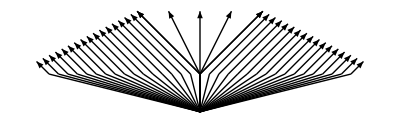

```mathematica
Show[Graphics[{
Arrowheads[Small],
Table[
Module[{x0={0,-2},T=4,t=-.1,y0,v0,ζ0,ζ2s,v2s},
y0={t0,0};
t=Subscript[γ, F1][y0-x0];
v0=(y0-x0)/t;
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F1][v0](* points in normal cone properly scaled *);
(* calculate refracted angles with optimality conditions *)
ζ2s=Subscript[RefractedNormals, F2][ζ0];
v2s=Select[discretize/@(𝒩̂)_(F2^°)/@ζ2s,NonNegative@Last@#&];


If[T>Subscript[γ, F1][y0-x0],
{Black,Line[{x0,y0}],Tooltip[Arrow[{y0,(y0+(T-Subscript[γ, F1][y0-x0])#)}],{ζ2s}]},
{Lighter@Gray,Line[{x0,y0}]}
]&/@v2s

],
{t0,-8,8,0.5}
]}]]
```

```mathematica
Show[Graphics[{
Arrowheads[Small],
Table[
Module[{a={1,1},n={1,1},x0={0,-2},T=3,t,y0,v0,ζ0,ζ2s,v2s},

y0={t0,(a.n-t0 n⟦1⟧)/ n⟦2⟧};
t=Subscript[γ, F1][y0-x0];
v0=(y0-x0)/t;
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F1][v0](* points in normal cone properly scaled *);
(* calculate refracted angles with optimality conditions *)
v2s=Select[discretize/@Subscript[RefractedVelocities, F2][ζ0,n],#.n≥1&];


If[T>Subscript[γ, F1][y0-x0],
{Black,Line[{x0,y0}],Arrow[{y0,(y0+(T-Subscript[γ, F1][y0-x0])#)}]},
{Lighter@Gray,Line[{x0,y0}]}
]&/@v2s

],
{t0,-4,8,0.5}
]}]]
```

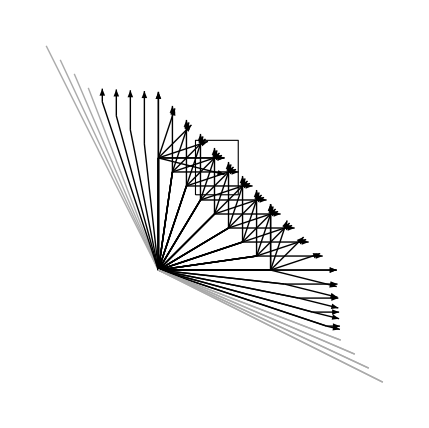

```mathematica
Manipulate[Show[Graphics[{
Arrowheads[Small],
Table[
Module[{a={Cos[θ],Sin[θ]},n={Cos[θ],Sin[θ]},x0={0,-0.5},T=3,t,y0,v0,ζ0,ζ2s,v2s},

y0={t0,(a.n-t0 n⟦1⟧)/ n⟦2⟧};
t=Subscript[γ, F1][y0-x0];
v0=(y0-x0)/t;
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F1][v0](* points in normal cone properly scaled *);
(* calculate refracted angles with optimality conditions *)
v2s=Select[discretize/@Subscript[RefractedVelocities, F2][ζ0,n],#.n≥1&];


If[T>Subscript[γ, F1][y0-x0],
{Black,Line[{x0,y0}],Arrow[{y0,(y0+(T-Subscript[γ, F1][y0-x0])#)}]},
Sequence[](*{Lighter@Gray,Line[{x0,y0}]}*)
]&/@v2s

],
{t0,-10,10,0.15}
]}]],{θ,0,2π}]
```

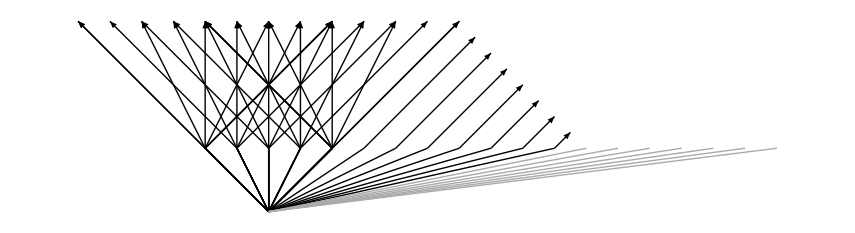

```mathematica
Show[Graphics[{
Arrowheads[Small],
Table[
Module[{a={0,1},n={0,1},x0={0,0},T=3,t,y0,v0,ζ0,ζ2s,v2s},

y0={t0,(a.n-t0 n⟦1⟧)/ n⟦2⟧};
t=Subscript[γ, F1][y0-x0];
v0=(y0-x0)/t;
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F1][v0](* points in normal cone properly scaled *);
(* calculate refracted angles with optimality conditions *)
v2s=Select[discretize/@Subscript[RefractedVelocities, F2][ζ0,n],#.n≥1&];


If[T>Subscript[γ, F1][y0-x0],
{Black,Line[{x0,y0}],Arrow[{y0,(y0+(T-Subscript[γ, F1][y0-x0])#)}]},
{Lighter@Gray,Line[{x0,y0}]}
]&/@v2s

],
{t0,-4,8,0.5}
]}]]
```

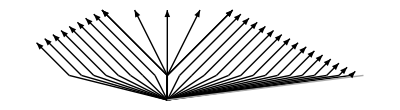

```mathematica
Show[Graphics[{
Arrowheads[Small],
Table[
Module[{a={0,1},n={0,2},x0={0,0},T=3,t,y0,v0,ζ0,ζ2s,v2s},

y0={t0,(a.n-t0 n⟦1⟧)/ n⟦2⟧};
t=Subscript[γ, F1][y0-x0];
v0=(y0-x0)/t;
(* Choose ζ0 ∈ Subscript[N, F0](v0) *)
ζ0=Subscript[𝒩̂, F1][v0](* points in normal cone properly scaled *);
(* calculate refracted angles with optimality conditions *)
v2s=Select[discretize/@Subscript[RefractedVelocities, F2][ζ0,n],#.n≥1&];


If[T>Subscript[γ, F1][y0-x0],
{Black,Line[{x0,y0}],Arrow[{y0,(y0+(T-Subscript[γ, F1][y0-x0])#)}]},
{Lighter@Gray,Line[{x0,y0}]}
]&/@v2s

],
{t0,-4,8,0.5}
]}]]
```

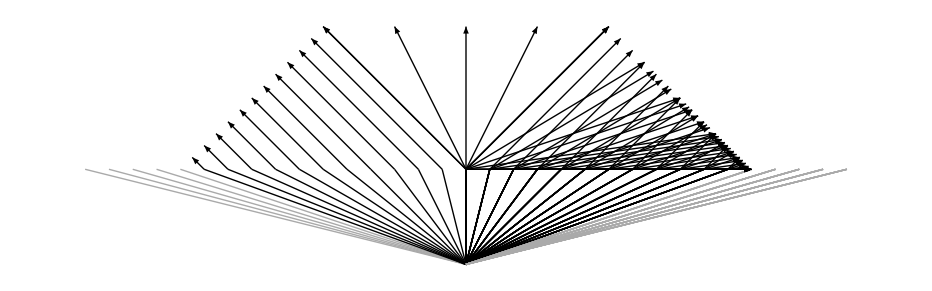

### Basic Functions (Initialization Cells)

#### Geometric Definitions

```mathematica
rotatedPairs[pts_]:=Partition[pts,2,1,1]
hullMagFunc[pts_]:=Function[{θ},
(* defines piecewise function for the magnitude of a convex hull (containing the origin) in the direction θ *)
Piecewise[{#2[θ],If[#1⟦1⟧≤#1⟦2⟧,#1⟦1⟧≤θ<#1⟦2⟧,-#1⟦1⟧≤θ<#1⟦2⟧]}&@@@(
{rotatedPairs[atan2/@pts],lineThroughPointsRFunc[#]&/@rotatedPairs[pts]}ᵀ)]]
```

```mathematica
hullToPolar[hull_]:={(#1⟦2⟧-#2⟦2⟧)/(#1⟦2⟧ #2⟦1⟧-#1⟦1⟧ #2⟦2⟧),(#1⟦1⟧-#2⟦1⟧)/(-#1⟦2⟧ #2⟦1⟧+#1⟦1⟧ #2⟦2⟧)}&@@@Partition[hull~Append~First@hull,2,1]
```

```mathematica
getThetaCnds[{p1_List,p2_List}]:=If[atan2[p1]<atan2[p2],atan2[p1]<θ<atan2[p2],atan2[p1]<θ<atan2[p2]+2π]
getThetaCnds[p1_]:=(θ==atan2[p1])
(* TODO: make proper dictionary *)
vζLink[F_]:=Function[{th},Piecewise[{(F^°)_pt~Join~(λ#1+(1-λ)#2&@@@RotateRight@rotatedPairs[(F^°)_pt]),getThetaCnds/@(rotatedPairs[Subscript[F, pt]]~Join~Subscript[F, pt])}ᵀ]/.{θ->th}]
ζvLink[F_]:=Function[{th},Piecewise[{RotateLeft@Subscript[F, pt]~Join~(λ#1+(1-λ)#2&@@@rotatedPairs[Subscript[F, pt]]),getThetaCnds/@(rotatedPairs[(F^°)_pt]~Join~(F^°)_pt)}ᵀ]/.{θ->th}]
```

```mathematica
ConeQ[x_]:=!FreeQ[x,λ]

DF=5;
discretize[x_]:=If[ConeQ[x],Sequence@@Table[x/.λ->t,{t,0,1,1/(DF-1)}],x]
```

#### Plot Definitions

```mathematica
PolarHullPlot[F_,styles___]:=Graphics[{
Blue,Thick,Line[{#1,#2}]&@@@rotatedPairs[(F^°)_pt],
Purple,Arrow[{{0,0},#}]&/@((F^°)_pt),
Line[{#1,#2}]&@@@rotatedPairs[Subscript[F, pt]],
Blue,PointSize[Large],Point/@(Subscript[F, pt]),
Gray,Thin,Dashed,Circle[]
},styles]
SmallPolarHullPlot[F_,styles___]:=Graphics[{
Blue,Thick,Line[{#1,#2}]&@@@rotatedPairs[(F^°)_pt],
Purple,PointSize[Large],Point/@((F^°)_pt),Line[{#1,#2}]&@@@rotatedPairs[Subscript[F, pt]],
Blue,Point/@(Subscript[F, pt]),
Gray,Thin,Dashed,Circle[]
},styles]
LabeledPolarHullPlot[F_,styles___Rule]:=Show[{
PolarHullPlot[F],
ListPlot[Join[
Callout[#1,Subscript[ζ, #2],Background->Purple,LabelStyle->White]&@@@({(F^°)_pt,Range@Length@(F^°)_pt}ᵀ),
Callout[#1,Subscript[v, #2],CalloutMarker->"Circle",Background->Blue,LabelStyle->White]&@@@({Subscript[F, pt],Range@Length@Subscript[F, pt]}ᵀ)
]]
},PlotRange->All,Axes->False,styles]
LabeledPolarHullPlot[F_,superScript_String,transform_,styles___Rule]:=Show[{
PolarHullPlot[F],
ListPlot[Join[
Callout[transform@#1,Subscript[ζ, #2]^superScript,Background->Purple,LabelStyle->Directive[Medium,Bold,White]]&@@@({(F^°)_pt,Range@Length@(F^°)_pt}ᵀ),
Callout[transform@#1,Subscript[v, #2]^superScript,Background->Blue,LabelStyle->Directive[Medium,Bold,White]]&@@@({Subscript[F, pt],Range@Length@Subscript[F, pt]}ᵀ)
],PlotStyle->Transparent]
},PlotRange->All,Axes->False,styles]

PolarPlot0[F_,styles___Rule]:=Graphics[{
Blue,Thick,Line[{#1,#2}]&@@@rotatedPairs[(F^°)_pt],
Purple,Arrow[{{0,0},#}]&/@((F^°)_pt),
Gray,Thin,Dashed,Circle[]
},styles]
LabeledPolarPlot[F_,superScript_String,transform_,styles___Rule]:=Show[{
Graphics[{
Blue,Thick,Line[transform/@{#1,#2}]&@@@rotatedPairs[(F^°)_pt],
Purple,Arrow[transform/@{{0,0},#}]&/@((F^°)_pt),
Gray,Thin,Dashed,Circle[]
},styles],
ListPlot[Join[
Callout[transform@#1,Subscript[ζ, #2]^superScript,Background->Purple,LabelStyle->Directive[Medium,Bold,White]]&@@@({(F^°)_pt,Range@Length@(F^°)_pt}ᵀ)
],PlotStyle->Transparent]
},PlotRange->All,Axes->False,styles]
```